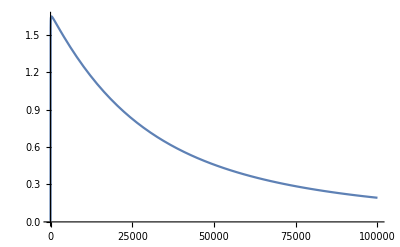

{-((R5 Vim+2 C2 f π R3 R5 Vim+2 C4 f π R3 R5 Vim+2 C5 f π R3 R5 Vim+2 C4 f π R4 R5 Vim+4 C2 C4 f^2 π^2 R3 R4 R5 Vim+4 C4 C5 f^2 π^2 R3 R4 R5 Vim+2 C5 f π R5 R6 Vim+4 C2 C5 f^2 π^2 R3 R5 R6 Vim+4 C4 C5 f^2 π^2 R3 R5 R6 Vim+4 C4 C5 f^2 π^2 R4 R5 R6 Vim+8 C2 C4 C5 f^3 π^3 R3 R4 R5 R6 Vim-R1 Vip-2 C3 f π R1 R2 Vip-R5 Vip-2 C1 f π R1 R5 Vip-2 C3 f π R1 R5 Vip-2 C3 f π R2 R5 Vip-4 C1 C3 f^2 π^2 R1 R2 R5 Vip-2 C5 f π R1 R6 Vip-4 C3 C5 f^2 π^2 R1 R2 R6 Vip-2 C5 f π R5 R6 Vip-4 C1 C5 f^2 π^2 R1 R5 R6 Vip-4 C3 C5 f^2 π^2 R1 R5 R6 Vip-4 C3 C5 f^2 π^2 R2 R5 R6 Vip-8 C1 C3 C5 f^3 π^3 R1 R2 R5 R6 Vip)/((R1+2 C3 f π R1 R2+2 C3 f π R1 R5+2 C3 f π R2 R5+4 C1 C3 f^2 π^2 R1 R2 R5) (1+2 C2 f π R3+2 C4 f π R3+2 C5 f π R3+2 C4 f π R4+4 C2 C4 f^2 π^2 R3 R4+4 C4 C5 f^2 π^2 R3 R4+2 C5 f π R6+4 C2 C5 f^2 π^2 R3 R6+4 C4 C5 f^2 π^2 R3 R6+4 C4 C5 f^2 π^2 R4 R6+8 C2 C4 C5 f^3 π^3 R3 R4 R6) (-Vim+Vip)))}

```mathematica
Module[{
R1=4420, R2=2320,R3=1330,
R4=715,R5=4990,R6=1500,
R7=560,R8=47000,
C1=2200 * 10^-12, C2=6.8*10^-9,
C3=470*10^-12, C4=22*10^-6,
C5=1.5*10^-9,C6=22*10^-6,
Vip=1.25,Vim=3.75
},
 Plot[Abs[Vo/Vi]/.Solve[
{
(Vim - e1)/R1 + (Vk-e1)/R5 +(Vm-e1)/R2 + (0-e1)/X[C1] == 0,
(e1 - Vm)/R2 == (Vm - Vk)/X[C3],
(Vip - e2)/R3+(0 -e2)/X[C2] + (0-e2)/ (R6+X[C5]) + (Vp-e2)/R4 == 0,
(e2 - Vp)/R4 == Vp/X[C4],
Vp == Vm,
Vi==Vip-Vim,
Vo == Vk*(R8/((R7+X[C6])+R8))
}, {Vm,Vp,e1,e2,Vk,Vi,Vo}],{f,0,100000}]]
```